π[n] = # prime numbers ≤ n;

Prime number theorem: lim_(n → ∞) π[n]/(n/ Log[n]) = 1

∃A,B,n_0: A> 0, B > 0, n_0>0  and
A  < π[n]/(n/Log[n]) < B , for n> n_0
Chebyshev(1852):0.92129 < π[n]/(n/Log[n]) < 1.10555

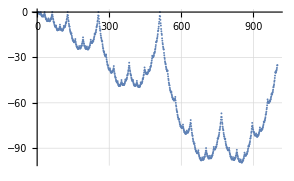
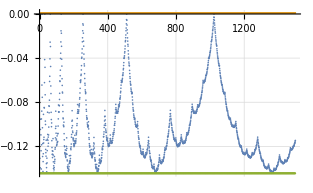

### lib

```mathematica
SetOptions[{ListPlot, Plot, LogLinearPlot,LogPlot},GridLines->Automatic];
```

```mathematica
FactorIntegerI[n_]:=Times@@(Subscript@@@FactorInteger[n]);
SetAttributes[FactorIntegerI,Listable];
```

```mathematica
IntTally[l_]:=Module[{t,v,f,nmax,res},
t=Tally[l];
nmax=Max[tᵀ⟦1⟧];
res=Table[0,{nmax+1}];
({t,f}=#; res⟦t+1⟧=f)&/@t;
res
];
```

### Catalan numbers

1) Counting objects is a fun. Combinatorics is a good starting point for learning math.
2) We easily discover asymptotics for Log[c_n]. It’s Log[4]n, so c_n≈4^n. 
 More precise formula:   c_n≈1/(√π)4^n/n^(3/2). Use Stirling’s approximation for n! to get it.
So we have one more (slow) formula for π approximation.
3) Formulas
	c_n=c_0 c_(n-1)+c_1 c_(n-2)+ ... +c_(n-1)c_0=∑_(i=0)^(n-1) c_i c_(n-i-1) ;
	c_n=((2n)!)/((n+1)(n!)^2)= (2n
n)1/(n+1);
	Recurrent formula  →  formula for generating function g[x] → explicit formula.
	Generating functions is useful tool!
	
4) TODO: Interesting behaviour of c_n mod p
      BTW: c_n is divided by all prime numbers between n+2 and 2n. !!!
      
5) Programming tasks c_n=? and IsCorrect[s ] and Generate[n] 
   are good tests for passion for programming and math.

## vp[c_p] and distribution of prime numbers

### c_n and b_n modulus prime, vp

c_n=(2n
n)1/(n+1);
b_n=(2n
n);

```mathematica
c[n_]:=Binomial[2n,n]/(n+1);
b[n_]:=Binomial[2n,n];
SetAttributes[c,{Listable}];
SetAttributes[b,{Listable}];
```

```mathematica
c[Range[10]]
```

```mathematica
b[Range[10]]
```

```mathematica
Table[Binomial[n,Range[0,n]],{n,0,10}]//TableForm
```

```mathematica
Table[If[n==2 i,Framed[Binomial[n,i]], Binomial[n,i],],{n,0,10},{i,0,n}]//TableForm
```

```mathematica
Mod[b[Range[70]],5]
```

vp[x, p] = power of p in factorization of x

```mathematica
vp[x_,p_]:=Module[{y=x,a=0},While[Mod[y,p]==0, a+=1; y/=p]; a];
SetAttributes[vp,Listable];
```

```mathematica
vp[b[Range[70]],5]
```

```mathematica
c[68]/125
```

```mathematica
vp[b[Range[470]],5]
```

b_n=((2n)!)/(n! n!);

vp[b_n, p] == vp[(2n)!, p] - 2vp[n!, p];

vp is completely additive arithmetic function.

### vp-identity

Log[x] = ∑_(p ∈ primes) Log[p] vp[x, p] 

We will apply this identity for
1. x = n!
2. x = b_n
2. x = b_1·b_2·... ·b_n

### vp[n!,p] and vp[b_n,p]

```mathematica
ListPlot[vp[Range[128],2], Filling->Bottom]
```

n = p^k;.01
vp[n!, p] == vp[1, p] + vp[2, p] + ... + vp[n, p] ==.01
			 ... change axis of summation ...
			== p^(k-1) + p^(k-2) + ... + 1;.01

vp[(2n)!, p] == 2 p^(k-1) + 2 p^(k-2) + .. + 2;

.01vp[((2n)!)/(n! n!), p] == 0  for n = p^k !!!.01  (p ∈Primes, p > 2)

PP = Prime Powers;.01

Log[n!] =∑_(p^k ∈ PP,
p^k ≤ n) ⌊n/p^k⌋  Log[p];.01     ⌊x⌋   stands for Floor[x].

n=p^k+a;   (vp[x, p] → vp[x])

vp[n!] == vp[1] + vp[2] + ... + vp[n] ==
			== p^(k-1) + p^(k-2) + .. + 1 +⌊a/p⌋+⌊a/p^2⌋+...+⌊a/p^k⌋

vp[(2n)!] == 2 p^(k-1) + 2 p^(k-2) + .. + 2+ ⌊(2a)/p⌋+⌊(2a)/p^2⌋+...+⌊(2a)/p^k⌋;

vp[((2n)!)/(n! n!),p] == ⌊(2a)/p⌋+⌊(2a)/p^2⌋+...+⌊(2a)/p^k⌋ - 2(⌊a/p⌋+⌊a/p^2⌋+...+⌊a/p^k⌋)
		== (⌊(2a)/p⌋- 2⌊a/p⌋) + (⌊(2a)/p^2⌋- 2⌊a/p^2⌋)+ (⌊(2a)/p^3⌋- 2⌊a/p^3⌋)+ ...;

```mathematica
⌊3.77⌋
```

```mathematica
Plot[Floor[2x]-2Floor[x],{x,0,1}]
```

```mathematica
ff[x_]:=Floor[2x]-2Floor[x];
```

```mathematica
Plot[ff[x/3],{x,0,3 3/2}]
```

```mathematica
Plot[ff[x/3] +ff[x/9],{x,0,9 3/2}]
```

```mathematica
Plot[ff[x/3] +ff[x/9] +ff[x/27],{x,0,27 3/2}]
```

Fractal - like function:

```mathematica
Plot[ff[x/3] +ff[x/9] +ff[x/27]+ff[x/81],{x,0,81 3/2}]
```

```mathematica
Plot[ff[x/5] ,{x,0,5},PlotPoints->300]
```

```mathematica
Plot[ff[x/5] +ff[x/25],{x,0,25 3/2},PlotPoints->300]
```

```mathematica
Plot[ff[x/5] +ff[x/25] +ff[x/125],{x,0,125 3/2},PlotPoints->300]
```

```mathematica
ListPlot[vp[b[Range[243]],3]]
```

```mathematica
ns=Range[4000]; p=3;
ListPlot[{vp[b[ns],p],Log[p,ns]+0.666}]
```

```mathematica
ns=Range[4000]; p=2;
ListPlot[{{Log[ns],vp[b[ns],p]}ᵀ,{Log[ns],Log[p,ns+1]}ᵀ}]
```

```mathematica
ns=Range[4000]; p =5;
ListPlot[{{Log[ns], vp[b[ns],p]}ᵀ,{Log[ns], Log[p,ns]+0.45}ᵀ}]
```

```mathematica
ns=Range[4000]; p =19;
ListPlot[{{Log[ns], vp[b[ns],p]}ᵀ,{Log[ns], Log[p,ns]+0.24}ᵀ}]
```

How many points at each horizontal lines? What is AVG y?
See next part “Frequencies  triangles” and “Formulas for Gxy and VpAvg for {b_n}”:

```mathematica
Clear[VpAvg];
VpAvg[k_,p_]:=k/2-1/(2 p^k)(p^k-1)/(p-1);
VpAvg[k_,2]:=k/(2 (1-2^-k));
```

### Frequencies triangles for vp[b_1·b_2·...·b_n,p] and their generating function

```mathematica
Tally[{1,2,101,101, 2, 2, 1,1,1,1}]
```

```mathematica
Tally[{4,1,1,2,7,7,7,2,2,2,0}]
```

```mathematica
IntTally[l_]:=Module[{t,v,f,nmax,res},
t=Tally[l];
nmax=Max[tᵀ⟦1⟧];
res=Table[0,{nmax+1}];
({t,f}=#; res⟦t+1⟧=f)&/@t;
res
];
```

```mathematica
IntTally[{4,1,1,2,7,7,7,2,2,2,0}]
```

```mathematica
p=2;
m=7; n=p^m-1;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally = IntTally[vps]
```

```mathematica
p=2;
(
m=#;  n=p^m-1;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally =IntTally[vps]
)&/@Range[1,8]//TableForm
```

```mathematica
Series[1/(1-y(1+x)),{y,0,5},{x,0,5}]//Normal
```

```mathematica
1/(1-y(1+x))-1/(1-y)//Together
```

```mathematica
Gxy[x_,y_, 2]:=x/((1-y)(1-y-x y));
```

```mathematica
Series[Gxy[x,y, 2],{y,0,5},{x,0,5}]//Normal
```

```mathematica
p=3;
(
m=#;  n=p^m;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally =IntTally[vps]
)&/@Range[0,8]//TableForm
```

We get this result in "How to get formulas for Gxy and VpAvg" → “Formulas for Gxy and VpAvg”

```mathematica
Gxy[x_,y_, p_]:=(1- x y)/(1-((p+1)(x+1))/2 y+p x y^2);
```

```mathematica
p=3;Series[Gxy[x,y, p],{y,0,5}]
```

### Accumulate vp[b_n,p]

#### Lower and upper bounds for vp[b_1 b_2 b_3 ... b_n]

```mathematica
ns=Range[1100];
```

```mathematica
ListPlot[{ns, Accumulate[vp[b[ns],2]]}ᵀ,GridLines->Automatic]
```

```mathematica
p=2; ns=Range[1000];
ListPlot[{
{ns, Log[p]Accumulate[vp[b[ns],p]] - 0.5Log[ns+1](ns+1)}ᵀ
},
GridLines->Automatic]
```

```mathematica
p=2;ns=Range[50];
ListPlot[{
{ns, (Log[p]Accumulate[vp[b[ns],p]] - 0.5Log[ns+1](ns+1))}ᵀ
},
GridLines->Automatic]
```

#### Minimums for p == 2

```mathematica
p=2;
ns=Range[500];
ListPlot[{
{ns, 1/ns(Log[p]Accumulate[vp[b[ns],p]] - 0.5Log[ns+1](ns+1))}ᵀ
},
GridLines->Automatic]
```

For p = 2
maximums at {1, 3, 7, 15, 31, ...} = {1,11_2,111_2, 1111_2,...}
minimums at {2,4, 10, 20, 42, 84, 170} = {10_2,100_2, 1010_2, 10100_2,  101010_2, 1010100_2, 10101010_2}

```mathematica
{2,4,10,20,42,84,170}//IntegerDigits[#,2]&
```

```mathematica
mins2={2,4,10,20,42,84,170, 170 * 2, 170 * 4 + 2}
```

```mathematica
p=2;
ns=Range[5000];
res2={ns, 1/ns(Log[p]Accumulate[vp[b[ns],p]] - 1/2 Log[ns+1](ns+1))}ᵀ[[
mins2
]]
```

```mathematica
res2//N
```

```mathematica
(bs={2,5,17,42,108,255,599,1364,3074})//IntegerDigits[#,2]&
```

For n=p^k-1 we have (see "Formulas for Gxy and VpAvg"):
vp[b_1 b_2 b_3 ... b_n,p]=∑_(m ≤ n = p^k-1) vp[b_m,p]== p^k(k/2-1/(2 p^k)(p^k-1)/(p-1))+k == (n+1)Log[p,n+1]/2-1/2 n/(p-1);

#### Upper and lower bounds

Bounds for vp[b_1 b_2 b_3 ... b_n,p]

```mathematica
MaxAccVp[n_,2]:=1/2((n+1) Log[2,n+1]); 
MinAccVp[n_,2]:=1/2((n+1) Log[2,n+1])-0.20744 n ;
```

In fact for p> 2 there is α_p:
MinAccVp[n_,p_]:=1/2((n+1) Log[p,n+1]-n/(p-1))- α_p n;
And α_p < 0.5.

```mathematica
1/2((n+1) Log[n+1]-(Log[p] n)/(p-1));
```

```mathematica
MaxAccVp[n_,p_]:=1/2((n+1) Log[p,n+1]-n/(p-1)); 
MinAccVp[n_,p_]:=1/2((n+1) Log[p,n+1]-n/(p-1))-0.5 n;
```

The first  minimum is at n_0 = (p-1)/2; 
vp[b_1 b_2 b_3 ... b_n_0,p] == 0;
So MaxAccVp[(p-1)/2,p] is the error of approximation MaxAccVp[n,p] at n = n_0

```mathematica
1/2((n+1) Log[n+1]-(Log[p] n)/(p-1));
```

```mathematica
Clear[n,p];n=(p-1)/2;
min0=MaxAccVp[n,p]//FullSimplify
```

```mathematica
Clear[p]; n= (p-1)/2;
Limit[MaxAccVp[n,p]/n ,p-> ∞]
```

Better virsion of MinAccVp:

```mathematica
ns=Range[16000];
lbp=(
p=#;
t=N[1/ns(Accumulate[vp[b[ns],p]] - MaxAccVp[ns,p])];
p-> -Min[t]
)&/@Append[Prime[Range[15]],71]
```

```mathematica
lb=Association[lbp];defLb=Max[Values[lbp]];
```

```mathematica
MinAccVp[n_,p_]:=MaxAccVp[n,p] - Lookup[lb,p,defLb] n;
```

```mathematica
p=7; ns=Range[4000];
ListPlot[{
{ns, 1/ns(Accumulate[vp[b[ns],p]] - MaxAccVp[ns,p])}ᵀ,
{ns,+0.001 + ns * 0 }ᵀ,
{ns,-0.001+1/ns(MinAccVp[ns,p] - MaxAccVp[ns,p])}ᵀ
},GridLines->Automatic,PlotRange->{Automatic,Automatic}]
```

```mathematica
Manipulate[
p=Prime[i]; ns=Range[4000];
ListPlot[{
{ns, 1/ns(Accumulate[vp[b[ns],p]] - MaxAccVp[ns,p])}ᵀ,{ns,+0.001 + ns * 0 }ᵀ,
{ns,-0.001+1/ns(MinAccVp[ns,p] - MaxAccVp[ns,p])}ᵀ
},
GridLines->Automatic,PlotRange->{Automatic,Automatic},
PlotLabel->"Prime p = " <> ToString[p],
AxesLabel->{"n", "(vp[SubscriptBox[b, 1] ..  SubscriptBox[b, n]]  -  (n + 1) Log[p, n + 1] - FractionBox[n, p - 1])/n"}
],
{{i,1},1,13,1}
]
```

#### Minimums for p == 3

```mathematica
p=3;
ns=Range[1000];
ListPlot[{
{ns, 1/ns(Accumulate[vp[b[ns],p]] -MaxAccVp[ns,p])}ᵀ,
{ns,+0.005+1/ns(MaxAccVp[ns,p] -  MaxAccVp[ns,p])}ᵀ,
{ns,-0.005+1/ns(MinAccVp[ns,p] -  MaxAccVp[ns,p])}ᵀ
},
GridLines->Automatic,PlotRange->{Automatic,Automatic}]
```

```mathematica
p=3;ns=Range[10000];
t3={ns, 1/ns(Accumulate[vp[b[ns],p]] - MaxAccVp[ns,p])}ᵀ;
```

Maximums for p == 3

```mathematica
p^Range[10]-1
```

```mathematica
p=3;
(p^Range[10]-1)//IntegerDigits[#,p]&
```

Minimums for p == 3

```mathematica
(mins3={13,40,121,364,1093,3280,9841})//IntegerDigits[#,3]&
```

```mathematica
t3[[mins3]]//N
```

```mathematica
t3[[mins3]]//Simplify
```

```mathematica
{45, 2 104,857,1644,12037, 2 21328,  147633}//IntegerDigits[#,p]&
```

#### Minimums for p == 5

```mathematica
p=5;
ns=Range[60];
ListPlot[{
{ns, 1/ns(Accumulate[vp[b[ns],p]] - MaxAccVp[ns,p])}ᵀ,
{ns,+0.001+1/ns(MaxAccVp[ns,p] -  MaxAccVp[ns,p])}ᵀ,
{ns,-0.001+1/ns(MinAccVp[ns,p] -  MaxAccVp[ns,p])}ᵀ
},
GridLines->Automatic,PlotRange->{Automatic,Automatic}]
```

```mathematica
p=5;
ns=Range[10000];
ListPlot[{
{ns, 1/ns(Accumulate[vp[b[ns],p]] - MaxAccVp[ns,p])}ᵀ,
{ns,+0.005+1/ns(MaxAccVp[ns,p] -  MaxAccVp[ns,p])}ᵀ,
{ns,-0.005+1/ns(MinAccVp[ns,p] -  MaxAccVp[ns,p])}ᵀ,
},
GridLines->Automatic]
```

```mathematica
ns=Range[10000];
t5={ns, 1/ns(Accumulate[vp[b[ns],p]] - MaxAccVp[ns,p])}ᵀ;
```

Maximums for p == 5

```mathematica
p=5;
p^Range[10]-1
(p^Range[10]-1)//IntegerDigits[#,p]&
```

Minimums for p == 5

```mathematica
(mins5={2,12,37,312,1562,7812})//IntegerDigits[#,5]&
```

```mathematica
t5[[mins5]]//N
```

```mathematica
t5[[mins5]]//Simplify
```

#### Minimums for p == 7

```mathematica
p=7;
ns=Range[160];
ListPlot[{
{ns, 1/ns(Accumulate[vp[b[ns],p]] - MaxAccVp[ns,p])}ᵀ,
{ns,+0.001+1/ns(MaxAccVp[ns,p] -  MaxAccVp[ns,p])}ᵀ,
{ns,-0.001+1/ns(MinAccVp[ns,p] -  MaxAccVp[ns,p])}ᵀ
},
GridLines->Automatic,PlotRange->{Automatic,Automatic}]
```

```mathematica
p=7;
ns=Range[27];
ListPlot[{
{ns, 1/ns(Accumulate[vp[b[ns],p]] - MaxAccVp[ns,p])}ᵀ,
{ns,+0.005+1/ns(MaxAccVp[ns,p] -  MaxAccVp[ns,p])}ᵀ,
{ns,-0.005+1/ns(MinAccVp[ns,p] -  MaxAccVp[ns,p])}ᵀ
},
GridLines->Automatic]
```

```mathematica
ns=Range[10000];
t7={ns, 1/ns(Accumulate[vp[b[ns],p]] - MaxAccVp[ns,p])}ᵀ;
```

Maximums for p == 7

```mathematica
p=7;
p^Range[10]-1
(p^Range[10]-1)//IntegerDigits[#,p]&
```

Minimums for p == 7

```mathematica
(mins7={3,24, 24 * 7 + 3, (24 * 7 + 3)7 + 3})//IntegerDigits[#,p]&
```

```mathematica
t7[[mins7]]//N
```

```mathematica
t7[[mins7]]//Simplify
```

#### other p

```mathematica
Prime[100]
```

```mathematica
p=541;
ns=Range[550];
ListPlot[{
{ns, 1/ns(Accumulate[vp[b[ns],2]] - MaxAccVp[ns,2])}ᵀ,
{ns, 1/ns(Accumulate[vp[b[ns],3]] - MaxAccVp[ns,3])}ᵀ,
{ns, 1/ns(Accumulate[vp[b[ns],5]] - MaxAccVp[ns,5])}ᵀ,
{ns, 1/ns(Accumulate[vp[b[ns],11]] - MaxAccVp[ns,11])}ᵀ,
{ns, 1/ns(Accumulate[vp[b[ns],19]] - MaxAccVp[ns,19])}ᵀ,
{ns, 1/ns(Accumulate[vp[b[ns],67]] - MaxAccVp[ns,67])}ᵀ,
{ns, 1/ns(Accumulate[vp[b[ns],173]] - MaxAccVp[ns,173])}ᵀ,
{ns, 1/ns(Accumulate[vp[b[ns],p]] - MaxAccVp[ns,p])}ᵀ,
{ns,-0.001+ns * 0}ᵀ,
{ns,-0.45+0*ns}ᵀ,
{ns,-0.5 + 0 * ns}ᵀ
},
GridLines->Automatic,PlotRange->{Automatic,Automatic}]
```

#### Plots of Log[p] vp[b_1 b_2 b_3 ... b_n]

```mathematica
ns=Range[10000];
```

```mathematica
ListPlot[{
{ns, Log[2]Accumulate[vp[b[ns],2]]}ᵀ,
{ns, Log[3]Accumulate[vp[b[ns],3]]}ᵀ,
{ns, Log[5]Accumulate[vp[b[ns],5]]}ᵀ,
{ns, Log[7]Accumulate[vp[b[ns],7]]}ᵀ,
{ns, Log[11]Accumulate[vp[b[ns],11]]}ᵀ,
{ns, Log[79]Accumulate[vp[b[ns],79]]}ᵀ,
{ns, Log[127]Accumulate[vp[b[ns],127]]}ᵀ,
{ns, Log[227]Accumulate[vp[b[ns],227]]}ᵀ
},
GridLines->Automatic]
```

```mathematica
ns=Range[5000];
```

```mathematica
ListPlot[{
{ns, 
+Log[2]Accumulate[vp[b[ns],2]]
+Log[3]Accumulate[vp[b[ns],3]]
+Log[5]Accumulate[vp[b[ns],5]]
+Log[7]Accumulate[vp[b[ns],7]]
+Log[11]Accumulate[vp[b[ns],11]]
+Log[13]Accumulate[vp[b[ns],13]]
}ᵀ,
{ns, Accumulate[Log[b[N[ns]]]]}ᵀ,
{ns, Log[2] ns^2}ᵀ
},GridLines->Automatic]
```

```mathematica
pm=Prime[400]
```

```mathematica
ListPlot[{
{ns, 400Log[pm]Accumulate[vp[b[ns],pm]]}ᵀ,
{ns, Accumulate[Log[b[N[ns]]]]}ᵀ
},GridLines->Automatic]
```

```mathematica
ns=Range[3000];
```

```mathematica
ListPlot[{
{ns, 
Plus@@((Log[#]Accumulate[vp[b[ns],#]])&/@Prime[Range[400]])
}ᵀ,
{ns, 400Log[pm]Accumulate[vp[b[ns],pm]]}ᵀ,
{ns, Accumulate[Log[b[N[ns]]]]}ᵀ
},GridLines->Automatic]
```

### Chebyshev inequalities and others. MAIN PART

#### π[n] ≥ 0.69 n/Log[n] from vp-identity for b_1 b_2 b_3 ... b_n

See  "Formulas for Gxy and VpAvg for {b_n}"

```mathematica
Clear[VpAvg];
VpAvg[k_,p_]:=k/2-1/(2 p^k)(p^k-1)/(p-1);
VpAvg[k_,2]:=k/(2 (1-2^-k));
```

```mathematica
k=7; p=2; n=p^k-1;
{vp[∏_(k=1)^n b[k],p], n VpAvg[k,2]}
```

```mathematica
k=2; p=11; n=p^k;
{vp[∏_(k=1)^n b[k],p],  n VpAvg[k,p]}
```

From "Accumulate vp" we experimentally get

	Log[p]vp[b_1 b_2 b_3 ... b_n, p] ≤ 1/2(n + 1)Log[n + 1]

In "Formulas for Gxy and VpAvg"  we confirmed this fact.

n! ≈ √(2 π n) (n/e)^n;
((2 n)!)/(n!)^2≈ (√(4 π n))/(√(2 π n))^2 (2n)^(2n)/n^(2n) = 1/(√π)4^n/n^(3/2);

or much simplier: ((2 n)!)/(n!)^2 < (1+1)^(2n)

(a) b_n≈1/(√π)4^n/n^(1/2) ; (from Stirling's approximation)
(b) b_n== ∏_(p ∈ primes
p ≤  b_n) p^vp[c_n, p]  ; (vp - identity);
"p ≤ b_n" could be replaced with "p ≤ 2n".

So
A. Log[b_1 b_2 b_3 ... b_n]~ ∑_(m  ≤  n) Log[1/(√π)4^m/m^(1/2)] 
			==  (n (n+1))/2 Log[4]- O[n Log[n]] ==
			==  n (n+1)Log[2]+ O[n Log[n]]

B. Log[b_1 b_2 b_3 ... b_n]== 
== ∑_(p ∈ Primes) Log[p]vp[b_1 b_2 ... b_n,p]==

≤  1/2∑_(p ≤  2n) (n+1) Log[n+1]  ==  ((n+1) Log[n+1])/2 π[2n];
From A and B we have: 
π[2n] ≥  2/((n+1) Log[n+1])( n (n+1)Log[2])==  (2n Log[2])/Log[n+1];

	π[2n] ≥ (2n Log[2])/Log[n+1];
	π[n] ≥ 0.69 n/Log[n]   starting from some n.

The prime number theorem:
lim_(n → ∞) π[n]/(n/Log[n])=1

is equivalent to

  lim_(n→ ∞) Log[b_n]/(Log[n] ∑_(p < 2n) 1) =  lim_(n→ ∞) (∑_(p < 2n) Log[p]vp[b_n,p])/(Log[n] ∑_(p < 2n) 1)= Log[2.0]

Explicit formulas and inequalities 
for vp[b_n,p] and vp[b_1·b_2...·b_n,p] 
could  shed the light on their AVG-values.

#### θ[n] = ∑_(p ≤ n) Log[p] ≤ 1.386 * n from b_n >∏_(n < p <= 2n) p

```mathematica
(1+x)^10//Expand
```

```mathematica
252 < 2^10
```

b_n=((2n)!)/(n! n!) < 2^(2n)

2^(2n)> b_n ≥ ∏_(p ∈ Primes
p ≥  n+1, p ≤ 2n) p;

Let's  denote

 θ[n] == Log[∏_(p ∈ Primes
p ≤ n) p] = ∑_(p ∈ Primes,
p ≤ n) Log[p];

Log[b_n] ≥  θ[2n]- θ[n];
so
Log[4] n ≥ ( θ[2n]- θ[n]);
Log[4] n/2 ≥ ( θ[n]- θ[n/2]);
Log[4] n/4 ≥ ( θ[n/2]- θ[n/4]);
....  
sum all above and get:
Log[4] 2 n ≥ θ[2n]

 θ[n] ≤ Log[4] n ≈ 1.386 * n ≈ α * n

But experimental fact is that:
 θ[n] =  n - n^(1/2) + n^(1/2) * noise. 
(watch video  18. Первый ноль ζ–функции).

#### π[n] ≤ 2.78 n/Log[n] from θ[n] ≤ 1.386 * n

Log[∏_(p ∈ Primes,
√n< p ≤ n) p] == θ[n] - θ[√n]

Log[√n] (π[n] - π[√n]) ≤ θ[n] - θ[√n]≤ θ[n]≤ α  n ;
π[n] - π[√n] ≤   (α n)/Log[√n] =(2 α n)/Log[n];

π[n]  ≤ (2 α n)/Log[n] +π[√n] ≤ (2 α n)/Log[n] + √n;

π[n]  ≤ (2.78 n)/Log[n]

#### vp-identity for n!: ψ_1[n] = Log[n] + O[1]

```mathematica
ListPlot[vp[Range[128],2], Filling->Bottom]
```

```mathematica
ListPlot[vp[Range[3^6],3], Filling->Bottom,PlotRange->All]
```

Definitions (again):

θ[n] == Log[∏_(p ∈ Primes
p ≤ n) p] == ∑_(p ∈ Primes,
p ≤ n) Log[p];

ψ[n] == ∑_(p^k ∈ Prime Powers
p^k ≤ n) Log[p];
ψ_1[n] == ∑_(p^k ∈ Prime Powers
p^k ≤ n) Log[p]/p^k;
Stirling's approximation:
Log[n!] ≈ n (Log[n] - 1) + O[Log[n]];

vp-identity for n!:
Log[n!] == ∑_(p^k ∈ PP,
p^k ≤ n) Log[p]  ⌊n/p^k⌋;        ⌊x⌋   stands for Floor[x]; {x} == x -⌊x⌋;
	== ∑_(p^k ∈ PP,
p^k ≤ n) Log[p] (n/p^k - {n/p^k})

	==n ∑_(p^k ∈ PP,
p^k ≤ n) Log[p]/p^k  - ∑_(p^k ∈ PP,
p^k ≤ n) Log[p] {n/p^k}


Log[n!] ≈ n ψ_1[n] - β ψ[n];  β ∈ (0, 1); 

But ψ[n] = θ[n] + θ[√n]+ θ[n^(1/3)] + θ[n^(1/4)] + ...;

Assume  θ[n] = α n  + o[n]
so
ψ[n] ≈ α n + α √n + α n^(1/3) + ... +o[n]≈ α n + o[n];

and vp-identity turns to

Log[n!] ≈ n ψ_1[n] - β (α n + o[n]);

ψ_1[n] ≈ (Log[n!] + β (α n + o[n]))/n;
ψ_1[n] ≈ (n (Log[n] - 1)+ o[Log[n]] + β (α n + o[n]))/n;

ψ_1[n] ≈ Log[n] - γ + o[1];
γ = 1 - α β;
Experimental facts: α = 1, γ = 0.57721566...

1-γ = lim_(n → ∞) (∑_(p^k ∈ PP,
p^k ≤ n) Log[p] {n/p^k})/(∑_(p^k ∈ PP,
p^k ≤ n) Log[p])=lim_(n → ∞) (∑_(p^k ∈ PP,
p^k ≤ n) Log[p] {n/p^k})/n

#### Experiment: ψ[n] = ∑_(p^k ≤ n) Log[p] ~ n, i.e. α = 1

ψ[n] ==∑_(p^k ∈ Prime Powers
p^k ≤ n) Log[p];

```mathematica
primes = Prime[Range[100000]];
n=primes⟦-1⟧;
psi = Plus@@((
p=N[#];
Log[p]Floor[Log[p,n]]
)&/@primes);
{n,psi}
```

experimental fact is that:
 ψ[n] = n + √n  noise. 
(watch  18. Первый ноль ζ–функции).
More precise:
 ψ[n] = n -Log[2 π]+1/(2 n^2)+√n noise

#### Experimental facts

Watch video 18. Первый ноль ζ – функции.
-Graphics-

ψ_1[n] =∑_(p^k ≤ n) Log[p]/p^k;
ψ[n] = ∑_(p^k ≤ n) Log[p] = θ[n] + θ[√n] + θ[n^(1/3)] + θ[n^(1/4)] + ..;
θ[n] = ∑_(p ≤ n) Log[p] = ψ[n] - ψ[√n] - ψ[n^(1/3)] - ψ[n^(1/5)] + ψ[n^(1/6)] + .. ;

(a) ψ_1[n] = Log[n] - γ + 1/(√n) noise_0

(b) ψ[n] = n + √n noise_1

(c) θ[n] = n - √n + √n noise_2

Let's check:

Log[n!] ≈ n ψ_1[n] - β ψ[n]; 

n(Log[n] - 1) + 1/2 Log[n] ≈ n(Log[n] - γ + 1/(√n)noise_0) - β (n + √n noise_1);
-1 == - γ - β

γ = 1 - β = 1 - lim_(n → ∞) (∑_(p^k ≤ n) Log[p] {n/p^k})/(∑_(p^k ≤ n) Log[p]) = 1 - lim_(n → ∞) (∑_(p^k ≤ n) Log[p] {n/p^k})/n

γ == EulerGamma == 0.57721566...

#### Some experiments with averaging Log[p] {n/p^k}

Lets experiment with 
lim_(n → ∞) (∑_(p^k ≤ n) Log[p] {n/p^k})/(∑_(p^k ≤ n) Log[p])
1. Subsets of primes.
2. Relace p^k to p

```mathematica
pps0=Range[100]//Select[#,PrimePowerQ]&;
pps = {FactorInteger[#]⟦1,1⟧,#}&/@pps0
```

```mathematica
n=10000000;
pps0=Range[n]//Select[#,PrimePowerQ]&;
pps = {FactorInteger[#]⟦1,1⟧,#}&/@pps0;
```

```mathematica
1- Plus@@(({p,pp}=#; Log[p](n/pp-Floor[n/pp]))&/@N[pps])/n
```

```mathematica
EulerGamma//N
```

```mathematica
n=Prime[1000000]
```

```mathematica
pps0=Range[n]//Select[#,PrimePowerQ]&;
pps = {FactorInteger[#]⟦1,1⟧,#}&/@pps0;
```

```mathematica
ppsF = Select[pps, #⟦1⟧ > 1&]; 
sumwx= Plus@@(({p,pp}=#; Log[p](n/pp-Floor[n/pp]))&/@N[ppsF]);
sumw = Plus@@(({p,pp}=#; Log[p])&/@N[ppsF]);
1-sumwx/sumw
```

```mathematica
⌊5.6⌋
```

```mathematica
ppsF = Select[pps, #⟦1⟧ > 2&]; 
sumwx= Plus@@(({p,pp}=#; Log[p](n/pp-Floor[n/pp]))&/@N[ppsF]);
sumw = Plus@@(({p,pp}=#; Log[p])&/@N[ppsF]);
1-sumwx/sumw
```

```mathematica
ppsF = Select[pps, #⟦1⟧ > 2000&]; 
sumwx= Plus@@(({p,pp}=#; Log[p](n/pp-Floor[n/pp]))&/@N[ppsF]);
sumw = Plus@@(({p,pp}=#; Log[p])&/@N[ppsF]);
1-sumwx/sumw
```

```mathematica
ps = Prime[Range[1000000]];
psF = Select[ps, # > 2&]; 
sumwx= Plus@@((p=#; Log[p](n/p-Floor[n/p]))&/@N[psF]);
sumw = Plus@@((p=#; Log[p])&/@N[psF]);
1-sumwx/sumw
```

```mathematica
ps = Prime[Range[1000000]];
psF = Select[ps, # < Prime[50000]&]; 
sumwx= Plus@@((p=#; Log[p](n/p-Floor[n/p]))&/@N[psF]);
sumw = Plus@@((p=#; Log[p])&/@N[psF]);
1-sumwx/sumw
```

### Formulas for Gxy and VpAvg for {b_n}. MAIN PART

#### Triangle for p = 2: distribution of values of vp[b_(p^k),p]

```mathematica
ns=Range[2^12-1];
Tally[vp[b[ns],2]]
```

```mathematica
ns=Range[2^12-1];
Tally[vp[c[ns],2]]
```

```mathematica
Binomial[12,Range[0,12]]
```

```mathematica
ListPlot[Tally[vp[b[ns],2]],GridLines->Automatic]
```

```mathematica
ListPlot[Tally[vp[c[ns],5]],GridLines->Automatic]
```

```mathematica
m=12;  n=2^m;
avg=m/2 ;
ns=Range[n];
s2=Sqrt[m];
vps=vp[b[ns],2];
 ListPlot[
{
{#⟦1⟧,#⟦2⟧ / n }&/@Tally[vps],
{#⟦1⟧, Binomial[m,#⟦1⟧]/2^m}&/@Tally[vps]
},
GridLines->Automatic
]
```

```mathematica
p=2;
m=8;  n=p^m-1;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally = Tally[vps]
```

```mathematica
IntTally[l_]:=Module[{t,v,f,nmax,res},
t=Tally[l];
nmax=Max[tᵀ⟦1⟧];
res=Table[0,{nmax+1}];
({t,f}=#; res⟦t+1⟧=f)&/@t;
res
];
```

```mathematica
p=2;
m=8;  n=p^m-1;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally = IntTally[vps]
```

```mathematica
p=2;
(
m=#;  n=p^m-1;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally =IntTally[vps]
)&/@Range[1,8]//TableForm
```

```mathematica
p=2;
(
m=#;  n=p^m-1;
ns=Range[n];
vps=vp[c[ns],p];
vpsTally =IntTally[vps]
)&/@Range[1,8]//TableForm
```

#### Triangle for p = 3, 5, 7

```mathematica
p=3;
t=(
m=#;  n=p^m;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally =IntTally[vps]
)&/@Range[0,8]//TableForm
```

-Graphics-;

```mathematica
1072 - {312, 130, 53,21,8,4}. {2,1,2,4,8,16}
```

-Graphics-;

```mathematica
1072 - {419, 130, 36, 8}. {2,1,2,4}
```

```mathematica
-Graphics-;
```

```mathematica
1072-{312,419, 448, 384, 256,128}.{2,1/2,3/8,3/16 ,3/128,-15/256}
```

-Graphics-;

```mathematica
1072-{312,130,159,58, 48, 16}.{2,1,1,3/2, 9/8,9/8}
```

```mathematica
384-{64,32,16,8,4,2,1,1}.{2,1,2,4,8,16,32,64}
```

```mathematica
384-{64,176,312,419,448,384,256,128}.{2,1/2,3/8,3/16 ,3/128,-15/256,-57/1024,-21/2048}
```

```mathematica
736-{176,312,419,448,384,256,128}.{2,1/2,3/8,3/16 ,3/128,-15/256,-57/1024}
```

```mathematica
176- {32,80,130,159,152,112,64}.{2,1/2,3/8,3/16 ,3/128,-15/256,-57/1024}
```

```mathematica
p=5;
m=6;  n=p^m;
ns=Range[n];
s2=Sqrt[m];
vps=vp[b[ns],p];
vpsTally = Tally[vps]
FactorIntegerI[vpsTallyᵀ⟦2⟧]
```

```mathematica
p=5;
(
m=#;  n=p^m;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally = IntTally[vps]
)&/@Range[0,6]//TableForm
```

```mathematica
1674 - {486, 54}.{3,4}
```

```mathematica
3150 - {794,138,18 }.{3,4,12}
```

```mathematica
3970-{794, 190,42, 9}.{3,4,12,36}
```

```mathematica
p=7;
(
m=#;  n=p^m;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally = IntTally[vps]
)&/@Range[0,5]//TableForm
```

```mathematica
768-{192}.{4}
```

```mathematica
2640-{552,48}.{4,9}
```

```mathematica
4539 - {777,111,12}.{4, 9, 9 * 4}
```

```mathematica
4764 - {624,120,21,3}.{4, 9, 9 * 4, 9 * 4^2}
```

#### Gxy for p = 2

```mathematica
p=2;
(
m=#;  n=p^m-1;
ns=Range[n];
vps=vp[b[ns],p];
IntTally[vps]
)&/@Range[1,8]//TableForm
```

```mathematica
gp2=1/(1-y-y x) ;
Series[gp2,{y,0,5}]
```

```mathematica
gb2=Together[(1/(1-y-y x) - 1/(1-y))/y]
```

```mathematica
gb2=x/((1-y) (1-y-x y));
```

```mathematica
Series[gb2,{y,0,5}]
```

#### VpAvg for p = 2

```mathematica
p=2;
m=5; n=p^m -1;ns=Range[n];
vps=vp[b[ns],p];
vpsTally =Tally[vps]
```

```mathematica
vpAvg = (1*5 + 2*10 + 3*10 + 4*5 + 5*1)/(5 + 10+10+ 5+1)
```

```mathematica
vpsG = Plus@@(#⟦2⟧ x^(#⟦1⟧)&/@vpsTally)
```

```mathematica
D[vpsG,x]/vpsG/.{x->1}
```

```mathematica
D[Log[vpsG],x]/.{x->1}
```

By the way: there is integral formula to extract  f_k[x] y^k from sum 
f_0[x] y^0+f_1[x] y^1+f_2[x] y^2+...

```mathematica
Clear[t];
expr=Integrate[1/(1-y-x y)y^-6 /.{y-> ⅇ^(2 ⅈ π t)},{t,0,1}]
```

```mathematica
avgx=D[Log[expr], x] ;
avgx/.{x->1.0}
```

```mathematica
Bn[k_,2]:=(1+x)^k-1;
```

```mathematica
Clear[k];
D[Log[Bn[k,2]],x]/.{x->1}
```

```mathematica
(2^(-1+k) k)/(-1+2^k)== 1/2 k/(1-2^-k)//FullSimplify
```

```mathematica
VpAvg[k_,2]:=1/2 k/(1-2^-k);
```

```mathematica
Plot[VpAvg[k,2]/k,{k,1,20}]
```

#### Gxy for p = 3

```mathematica
p=3;
(
m=#;  n=p^m;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally =IntTally[vps]
)&/@Range[0,8]//TableForm
```

-Graphics-;

```mathematica
1072 - {312, 130, 53,21,8,4 }. {2,1,2,4,8,16}
```

F[x,y] = y^0 f_0[x] + y^1 f_1[x]+y^2 f_3[x]+ ...

  = 1 + y (2 + x) + y^2(4 + 3x + 2 x^2)+y^3(8 + 8x + 7 x^2+4 x^3)+...;

f_n[x] == 2 f_(n-1)[x] +  x f_(n-2)[x] + 2 x^2 f_(n-3)[x] + 4 x^3 f_(n-4)[x] + 8 x^4 f_(n-5)[x] +...

F[x,y] ==1 + (y x)/(1-2 x y) + 2 y F[x,y] + y^2 x F[x,y] + 2 y^3 x^2  F[x,y] + ...;
F[x,y] (1-2y - (y^2 x)/(1-2y x) ) =1 + (y x)/(1-2 x y) ;

F[x,y] = (1+ (y x)/(1-2 y x))/(1-2y - (y^2 x)/(1-2y x))

```mathematica
ff3=1 + y (2 + x) + y^2(4 + 3x + 2 x^2)+y^3(8 + 8x + 7 x^2+4 x^3) ;
```

```mathematica
1 + (y x)/(1-2 x y)  + 2y ff3  + y^2 x ff3 + y^3 2 x^2 ff3 + y^4 4 x^3 ff3//Series[#,{y,0,4}]&//Expand//Collect[#,y]&
```

```mathematica
(1+ (y x)/(1-2 y x))/(1-2y - (y^2 x)/(1-2y x)) //Together
```

```mathematica
gb3=(1-x y)/(1-2 y-2 x y+3 x y^2);
```

```mathematica
Series[gb3,{x,0,7},{y,0,7}]//Normal//Expand//Collect[#,y]&
```

#### VpAvg for p = 3 (fail)

```mathematica
p=3;
m=5;  n=p^m;ns=Range[n];
vps=vp[c[ns],p];
vpsTally =Tally[vps]
```

```mathematica
vpAvg = (0*48+1*60 + 2*63 + 3*48 + 4*24)/(48+60+63+48+24)
```

```mathematica
vpsG = Plus@@(#⟦2⟧ x^(#⟦1⟧)&/@vpsTally)
```

```mathematica
D[vpsG,x]/vpsG/.{x->1}
```

```mathematica
D[Log[vpsG],x]/.{x->1}
```

```mathematica
gxy3=(1-x y)/(1-2 y-2 x y+3 x y^2);
expr=Integrate[gxy3 y^-6/.{y-> ⅇ^(2 ⅈ π t)},{t,0,1}]
```

See “Formulas for Gxy and VpAvg”

#### Gxy for p = 5, 7, 11

```mathematica
p=5;
(
m=#;  n=p^m;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally = IntTally[vps]
)&/@Range[0,4]//TableForm
```

```mathematica
gb5=(1- x y)/(1-3 y-3 x y+5 x y^2);
Series[gb5,{y,0,5}]
```

```mathematica
p=7;
(
m=#;  n=p^m;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally = IntTally[vps]
)&/@Range[0,4]//TableForm
```

```mathematica
gb7=(1- x y)/(1-4 y-4 x y+7 x y^2);
Series[gb7,{y,0,5}]
```

For n= p^k-1:

```mathematica
p=7;
(
m=#;  n=p^m-1;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally = IntTally[vps]
)&/@Range[1,4]//TableForm
```

```mathematica
ggb7=(1- x y)/(1-4 y-4 x y+7 x y^2)-1/(1-y)//Together
```

```mathematica
ggb5=(1- x y)/(1-3 y-3 x y+5 x y^2)-1/(1-y)//Together
```

```mathematica
p=11;
(
m=#;  n=p^m;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally = IntTally[vps]
)&/@Range[0,4]//TableForm
```

```mathematica
gb11=(1- x y)/(1-6 y-6 x y+11 x y^2);
Series[gb11,{y,0,5}]
```

#### Formulas for Gxy and VpAvg (success)

n=p^k, Tally[{vp[b_i]}_(i=1...n)] - k-th line in triangle;

Generating function for this triangle:
          Gxy[x,y]== (1- x y)/(1-((p+1)(x+1))/2 y+p x y^2)     (p ≥ 3)

Tally[{vp[c_i]}_(i=1...n)] - k-th line in triangle;
         Gxy[x,y]== (1+y-2 x y)/(1-((p+1)(x+1))/2 y+p x y^2)    (p > 3)

```mathematica
Gxy[x_,y_, p_]:=(1- x y)/(1-((p+1)(x+1))/2 y+p x y^2);
```

```mathematica
Clear[p];
{y1,y2}=y/.Solve[1-(p+1)/2 y(x+1)+p x y^2==0, y]
```

```mathematica
1/(p x(y1-y2))(1/(y-y1)-1/(y-y2))==1/(1-((p+1)(x+1))/2 y+p x y^2)//FullSimplify
```

```mathematica
(1- x y)/(p x(y1-y2))(1/(y-y1)-1/(y-y2))==(1- x y)/(1-((p+1)(x+1))/2 y+p x y^2)//FullSimplify
```

```mathematica
p=5;
Series[(1- x y)/(1-((p+1)(x+1))/2 y+p x y^2),{y,0,5},{x,0,5}]
```

```mathematica
p=5;
Series[1/(1-((p+1)(x+1))/2 y+p x y^2),{y,0,5},{x,0,5}]
```

```mathematica
Clear[n,p,Fn];
Fn[k_,p_]:=Evaluate[1/(p x(y1-y2))(  (1/y2)^(k+1) -(1/y1)^(k+1))//Together//FullSimplify];

Bn[k_,p_]:=Fn[k,p] - x Fn[k-1,p];
```

```mathematica
Fn[4,5]//FullSimplify//Expand
```

```mathematica
Fn[3,5]//FullSimplify//Expand
```

```mathematica
Bn[4,5]//FullSimplify//Expand
```

```mathematica
avgF = (0 81+1 189 x+2 241 x^2+3 189 x^3+4 81 x^4)/(81+189 x+241 x^2+189 x^3+81 x^4) /.{x->1}
```

```mathematica
Clear[k, p];
expr0=D[Log[Fn[k,p] ],x];
avg=expr0/.{x->1};
```

```mathematica
Assuming[p-1>0,FullSimplify[avg]]
```

```mathematica
avgB  =(0 81+1 162 x+2 190 x^2+3 138 x^3+4 54 x^4)/(81+162 x+190 x^2+138 x^3+54 x^4) /. {x->1}
```

```mathematica
Clear[k, p];
exprB=D[Log[Bn[k,p] ],x];
avgB=exprB/.{x->1};
```

```mathematica
avgB/.{k->4, p-> 5}
```

```mathematica
Assuming[p-1>0,FullSimplify[avgB]]
```

```mathematica
k/2-1/(2 p^k)(p^k-1)/(p-1)== (1+k-k p-p^-k)/(2-2 p)//FullSimplify
```

```mathematica
Clear[VpAvg];
VpAvg[k_,p_]:=k/2-1/(2 p^k)(p^k-1)/(p-1);(* for n = p^k *)
VpAvg2[k_,p_]:=k/(2(1 - p^-k))-1/2 1/(p-1);(* for n = p^k -1 *)
VpAvg[k_,2]:=k/(2 (1-2^-k)); (* for n = 2^k - 1 *)

AccVp[k_,p_]:=1/2 (p^k k)-1/2(p^k-1)/(p-1);
AccVp[k_,2]:=1/2(2^k k);
```

For n=p^k and n=p^k-1  (for  p > 2) 
vp[b_1 b_2... b_n] are the same because
           vp[b_(p^k),p] =vp[((2 p^k)!)/((p^k! )^2),p]=0.
vp[b_1 b_2... b_(p^k-1)] == vp[b_1 b_2... b_(p^k-1)b_(p^k)] == AccVp[k,p];
Fo n = p^k-1 we have 
	vp[b_1 b_2... b_n,p] =  1/2(n+1)Log[p,n+1]-1/2 n/(p-1), for p > 2;
	vp[b_1 b_2... b_n,2] =  1/2(n+1)Log[2,n+1];
For other n  "≤" should be used instead of "=":
	vp[b_1 b_2... b_n,p] ≤   1/2(n+1)Log[p,n+1]-1/2 n/(p-1), for p > 2;
	  vp[b_1 b_2... b_n,2] ≤   1/2(n+1)Log[2,n+1];

```mathematica
Clear[k];
lines=(p=#; VpAvg[k,p]/k)&/@ {2, 3,5,7,11,19,59};

Plot[lines,{k,1,50},PlotRange->{Automatic,{0,0.9}}]
```

```mathematica
gb5=(1-x y)/(1-3 y-3 x y+5 x y^2)
```

```mathematica
gb5//Series[#,{y,0,5}]&
```

Let' s self check

```mathematica
p=5; k=5; n=5^k;
(Plus@@Table[vp[b[i],5],{i,n}])/n
```

```mathematica
g=243+594 x+846 x^2+794 x^3+486 x^4+162 x^5;
D[Log[g],x] /. {x->1}
```

```mathematica
VpAvg[5,5]
```

### Gxy for {c_n}

#### Gxy for p = 2

n=2^m-1

```mathematica
ns=Range[2^12-1];
Tally[vp[c[ns],2]]
```

```mathematica
Binomial[12,Range[12]]
```

```mathematica
p=2;
m=8;  n=p^m-1;
ns=Range[n];
vps=vp[c[ns],p];
vpsTally = Tally[vps]
```

```mathematica
p=2;
(
m=#;  n=p^m-1;
ns=Range[n];
vps=vp[c[ns],p];
vpsTally =IntTally[vps]
)&/@Range[1,8]//TableForm
```

```mathematica
gc2=(1/x)/(1-y - x y)-(1/x)/(1-y)//Together
```

```mathematica
{vp[c[1], 2], vp[c[2], 2], vp[c[3], 2]}
```

```mathematica
Series[gc2,{y,0,7}]//Normal//Expand//Collect[#,y]&
```

#### Gxy for p = 3

n=p^m

```mathematica
p=3;
(
m=#;  n=p^m;
ns=Range[n];
vps=vp[c[ns],p];
vpsTally =IntTally[vps]
)&/@Range[1,8]//TableForm
```

Divide by 3

```mathematica
p=3;
(
m=#;  n=p^m;
ns=Range[n];
vps=vp[c[ns],p];
vpsTally =IntTally[vps]/3
)&/@Range[1,8]//TableForm
```

-Graphics-;

```mathematica
1072 - {312, 130, 53,21,8,4 }. {2,1,2,4,8,16}
```

F[x,y] = y^0 f_0[x] + y^1 f_1[x]+y^2 f_3[x]+ ...

  = 1 + y (2 + x) + y^2(4 + 3x + 2 x^2)+y^3(8 + 8x + 7 x^2+4 x^3)+...;

f_n[x] == 2 f_(n-1)[x] +  x f_(n-2)[x] + 2 x^2 f_(n-3)[x] + 4 x^3 f_(n-4)[x] + 8 x^4 f_(n-5)[x] +...

F[x,y] ==1 + (y x)/(1-2 x y) + 2 y F[x,y] + y^2 x F[x,y] + 2 y^3 x^2  F[x,y] + ...;
F[x,y] (1-2y - (y^2 x)/(1-2y x) ) =1 + (y x)/(1-2 x y) ;

F[x,y] = (1+ (y x)/(1-2 y x))/(1-2y - (y^2 x)/(1-2y x))

```mathematica
ff3=1 + y (2 + x) + y^2(4 + 3x + 2 x^2)+y^3(8 + 8x + 7 x^2+4 x^3) ;
```

```mathematica
1+y x +2 y^2 x^2 + 4 y^3 x^3  + 2y ff3  + y^2 x ff3 + y^3 2 x^2 ff3 + y^4 4 x^3 ff3//Expand//Collect[#,y]&
```

```mathematica
(1+ (y x)/(1-2 y x))/(1-2y - (y^2 x)/(1-2y x)) //Together
```

```mathematica
vp[c[1]c[2] c[3], 3]
```

```mathematica
vp[c[1]c[2] c[3]c[4]c[5], 5]
```

```mathematica
gc3=(3(1-x y)y)/(1-2 y-2 x y+3 x y^2) +1//Together
```

```mathematica
Series[gc3,{x,0,7},{y,0,7}]//Normal//Expand//Collect[#,y]&
```

#### Gxy for p = 5

```mathematica
p=5;
(
m=#;  n=p^m;
ns=Range[n];
s2=Sqrt[m];
vps=vp[c[ns],p];
vpsTally = Tally[vps]ᵀ⟦2⟧
)&/@Range[0,6]//TableForm
```

```mathematica
3970-{794, 190,42, 9}.{3,4,12,36}
```

F[x,y] = y^0 f_0[x] + y^1 f_1[x]+y^2 f_3[x]+ ...

  = 1 + y (4 + x) + y^2(12 + 10x + 3 x^2)+y^3(36 + 46x + 34 x^2+9 x^3)+...;

f_n[x] == 3 f_(n-1)[x] +  4 x f_(n-2)[x] + 12 x^2 f_(n-3)[x] + 36 x^3 f_(n-4)[x] + 108 x^4 f_(n-5)[x] +...

F[x,y] ==1 + (y + y x)/(1-4 x y) + 3 y F[x,y] + 4 y^2 x F[x,y] + 12 y^3 x^2  F[x,y] + ...;
F[x,y] (1-3y - (4 y^2 x)/(1-3y x) ) =1 + (y + y x)/(1-3 x y);

F[x,y] = (1 + (y + y x)/(1- 3 x y))/(1-3y - (4 y^2 x)/(1 - 3y x))

```mathematica
ff5=1 +    y (4 + x) + y^2(12 + 10x + 3 x^2)+y^3(36 + 46x + 34 x^2+9 x^3);
Series[1 +y + y x  + 3 y^2 x  + 3 y^2 x^2 + 9 y^3 x^2  + 9 y^3 x^3   + 3 y ff5 + 4 y^2 x ff5 + 12 y^3 x^2 ff5,{x,0,5},{y,0,5}]//Normal//Collect[#,y]&
```

```mathematica
(1 + (y + y x)/(1- 3 x y))/(1-3y - (4 y^2 x)/(1-3y x))//Together
```

```mathematica
gc5=(1+y-2x y)/(1-3 y-3 x y+5 x y^2);
Series[gc5, {x,0,7},{y,0,7}]//Normal//Collect[#,y]&
```

#### Gxy for p = 7

```mathematica
p=7;
(
m=#;  n=p^m;
ns=Range[n];
s2=Sqrt[m];
vps=vp[c[ns],p];
vpsTally = Tally[vps]ᵀ⟦2⟧
)&/@Range[0,5]//TableForm
```

```mathematica
3504 - 4 696 - 9 80
```

```mathematica
4989 - 4 777 - 9 129 - 36 20
```

F[x,y] = y^0 f_0[x] + y^1 f_1[x]+y^2 f_3[x]+ ...

  = 1 + y (5 + 2x) + y^2(20 + 21x + 8 x^2)+y^3(80 + 129x + 102 x^2+32 x^3)+...;

f_n[x] == 4 f_(n-1)[x] +  9  x f_(n-2)[x] + 36 x^2 f_(n-3)[x] + 144 x^3 f_(n-4)[x] + 576 x^4 f_(n-5)[x] +...

F[x,y] ==1 + (y + 2y x)/(1-4 x y) + 4 y F[x,y] + 9 y^2 x F[x,y] + 36 y^3 x^2  F[x,y] + ...;
F[x,y] (1-4y - (9 y^2 x)/(1-4y x) ) =1 + (y + 2 y x)/(1-4 x y);

F[x,y] = (1 + (y + 2 y x)/(1-4 x y))/(1-4y - (9 y^2 x)/(1-4y x))

```mathematica
ff7 = 1 + y (5 + 2x) + y^2(20 + 21x + 8 x^2)+y^3(80 + 129x + 102 x^2+32 x^3);

Series[1 + (y + 2y x)/(1-4 x y) + 4 y ff7 + 9 y^2 x ff7 + 36 y^3 x^2  ff7,{x,0,6},{y,0,7}]//Normal//Collect[#,y]&
```

```mathematica
gc7=(1 + (y + 2 y x)/(1-4 x y))/(1-4y - (9 y^2 x)/(1-4y x))//Together
```

```mathematica
{ff2,ff3, ff5, ff7}
```

#### Gxy for p = 11

```mathematica
p=11;
(
m=#;  n=p^m;
ns=Range[n];
s2=Sqrt[m];
vps=vp[c[ns],p];
vpsTally = Tally[vps]ᵀ⟦2⟧
)&/@Range[0,4]//TableForm
```

```mathematica
1512==6 252
```

```mathematica
4080 - 6 505 - 25 42
```

```mathematica
5005 - 6 430 - 25 55 - (25 6) 7
```

F[x,y] = y^0 f_0[x] + y^1 f_1[x]+y^2 f_3[x]+ ...

  = 1 + y (7 + 4x) + y^2(42 + 55x + 24 x^2)+y^3(252 + 505x + 430 x^2+144 x^3)+...;

f_n[x] == 6 f_(n-1)[x] +  25  x f_(n-2)[x] + 25 6 x^2 f_(n-3)[x] + 25 6 6 x^3 f_(n-4)[x] +...

F[x,y] ==1 + (y + 2y x)/(1-6 x y) + 4 y F[x,y] + 9 y^2 x F[x,y] + 36 y^3 x^2  F[x,y] + ...;
F[x,y] (1-6y - (25 y^2 x)/(1-6y x) ) =1 + (y + 4 y x)/(1-6 x y);

F[x,y] = (1 + (y + 2 y x)/(1-6 x y))/(1-6y - (25 y^2 x)/(1-6y x))

```mathematica
ff11 = 1 + y (7 + 4x) + y^2(42 + 55x + 24 x^2)+y^3(252 + 505x + 430 x^2+144 x^3) + y^4(1512 + 4080 x + 5005 x^2+3180 x^3+864 x^4)+ O[y]^5;

Series[1 + (y + 4 y x)/(1-6 x y) + 6 y ff11 + 25 y^2 x ff11 + 25 6 y^3 x^2  ff11 +25 6 6  y^4 x^3  ff11,{y,0,5}]//Normal//Collect[#,y]&
```

```mathematica
gc11=(1 + (y + 4 y x)/(1-6 x y))/(1-6y - (25 y^2 x)/(1-6y x))//Together
```

```mathematica
Series[gc11,{y,0,5}]
```

#### summary

```mathematica
{gc2,gc3, gc5, gc7, gc11}
```

```mathematica
GCxy[x_,y_,p_]:=(1+y-2 x y)/(1-((p+1) (x+1))/2 y+p x y^2) ;
GCxy[x_,y_,2]:=y/((y-1) (1-y-x y));
```

### Log[n!]/n is "partial sum" for ∂_s Log[ζ[s]]

Log[n!] == ∑_(p^k ∈ PP,
p^k ≤ n) Log[p] [n/p^k] ;
ψ_1[n] == ∑_(p^k ∈ PP
p^k ≤ n) Log[p]/p^k;
Log[n!] = n ψ_1[n] + O[n];

BTW: 

Log[ζ[s]] ==  Log[∏_(p ∈ Primes) 1/(1-1/p^s)];

Log[ζ[s]] == -∑_(p ∈ Primes) Log[1-1/p^s];


∂_s Log[ζ[s]] ==    ∑_(p ∈ Primes) (Log[s]1/p^s)/(1-1/p^s) ==
				==    ∑_(p ∈ Primes) Log[s](1/p^s + 1/p^(2s) + 1/p^(3s) + ...)  ==

				==∑_(p^k ∈ Prime Powers) Log[p]/p^(k*s)

### Takeaways

1. Numbers b_n=(2n
n) and c_n=(2n
n)1/(n+1) can give insights about arithmetic functions  π[n],θ[n],ψ[n],ψ_1[n].

π[n]=∑_(p ∈ Primes,
p ≤ n) 1;
θ[n]=∑_(p ∈ Primes,
p ≤ n) Log[p];           θ_m[n] =∑_(p ∈ Primes,
p ≤ n) Log[p]/p^m;

ψ[n]=∑_(p^k ∈ Prime Powers,
p^k ≤ n) Log[p];      ψ_m[n] =∑_(p^k ∈ Prime Powers,
p^k ≤ n) Log[p]/p^(k·m);

We use simple identity:  x = p_1^v_1·p_2^v_2·p_3^v_3... 
      Log[x] = ∑_(p ∈ primes) Log[p]  vp[x, p]     (vp-identity, it’s wrong my name, do not use it)
We use generating functions for triangles.

Gxy[x,y]== (1- x y)/(1-((p+1)(x+1))/2 y+p x y^2) 


2. Now we know how to prove  π[n]== A[n] n/Log[n];     A[n] ∈(0.69, 2.78) starting from some n. 
In fact,  there is limit A[n] → 1 as n → ∞. It’s  https://en.wikipedia.org/wiki/Prime_number_theorem
The theorem was proved independently by Jacques Hadamard and Charles Jean de la Vallée Poussin in 1896 using ideas introduced by Bernhard Riemann (in particular, the Riemann zeta function). Chebyshev proved that if limit exists then it is equal to 1.

3. vp[b_n, p] could be the subject of further investigations. Function vp[x, p]  =  power of p in factorization of x.
There are analytic lower and upper bounds for vp[b_1 b_2... b_n,p]: 
upper = 1/2((n+1) Log[p,n+1]-n/(p-1))
lower = 1/2((n+1) Log[p,n+1]-n/(p-1))- δ_p*n
So, sums   Log[p]* ∑ _(m=1)^n vp[b_m,p]  demonstrate same grouth rate  ∼1/2 n Log[n]  for all p.  
Primes p = 2 and p = 3 are special cases.

4. More systematic and classical way (using Abel' s partial summation formula) :
 https://www.youtube.com/playlist?list = PLhkiT_RYTEU1H7OmRVF5VJi76D2Efwf7F
An introduction to analytic number theory
-Graphics-
Stirling's approximation also could be obtained via Abel's partial summation formula.

### test

```mathematica
vp[x_,p_]:=Module[{y=x,a=0},While[Mod[y,p]==0, a+=1; y/=p]; a];
SetAttributes[vp,Listable];
```

```mathematica
b[n_]:=Binomial[2n, n];
```

Log[b_1... b_n]≈n^2/2 Log[4]=n^2 Log[2]

Log[b_1... b_n]=1/2∑_p ((n+1)Log[n+1] -n Log[p]/(p-1)-  n *Log[p]*ξ_(p,n) )  ,   ξ_(p,n) ∈ (0, 1.0) 
Log[b_1... b_n]  ≈1/2(n+1)Log[n+1] ∑_p 1  -n 1/2∑_(p>2) Log[p]/(p-1) -M_n/2 n∑_p Log[p] ,  M_n ∈ (0, 1.0)
Log[b_1... b_n]  ≈1/2 π[2n](n+1)Log[n+1]  -n 1/2 θ_*[2n] -M_n/2 n θ[2n],
Log[b_1... b_n]  ≈(n (n+1))/Log[2n] Log[n+1] -n^2 M_n 
Log[b_1... b_n]  ≈n^2-n^2 M_n    

so:
n^2 Log[2] ≈n^2-n^2 M_n 
M_n→(1-Log[2])=0.30685... 

OR split into p ∈ [1, n] and p ∈ [n+1, 2n]:
Log[b_1... b_n]  ≈1/2 π[n](n+1)Log[n+1]   -K_n/2 n θ[n] + ∑_(p>n) Log[p] (n-(p-1)/2),
Log[b_1... b_n]  ≈1/2 π[n](n+1)Log[n+1]   -K_n/2 n θ[n] +(n+1/2) (θ[2n] - θ[n]) - 1/2 ∑_(p>n) Log[p] p,
Log[b_1... b_n]  ≈1/2 π[n](n+1)Log[n+1]   -K_n/2 n θ[n] +(n+1/2) (θ[2n] - θ[n]) - 1/2 (θ_-1[2n] - θ_-1[n]),

n^2 Log[2]  ≈1/2 n^2  -K_n/2 n^2  +n^2- 1/2 (θ_-1[2n] - θ_-1[n]),
n^2 Log[2]  ≈1/2 n^2  -K_n/2 n^2  +n^2- 1/2 ((2n)^2/2 - n^2/2),
n^2 Log[2]  ≈1/2 n^2  -K_n/2 n^2  +n^2- 3/4 n^2,
K_n →2(3/4-Log[2]) = 0.1137...

```mathematica
1 - Log[2.0]
```

```mathematica
2(3/4 - Log[2.0])
```

```mathematica
primes1m=Prime[Range[1000000]];
```

```mathematica
n=1333;
primes2n=Select[primes1m, #≤ 2n&];
y=Log[b[n]]//N
{1/2 PrimePi[2n] (n Log[1+1/n] +Log[n+1] )/y,   Sump[primes2n]//N}
```

```mathematica
n=550;
primes2n=Select[primes1m, #≤ 2n&];
y=Plus@@((Log[b[#]])&/@N[Range[n]])
{1/2 PrimePi[2n] ((n+1) Log[n+1] )/y,  n Sump[primes2n]/y}
```

```mathematica
FactorInteger[127]
```

```mathematica
Clear[A0]
```

```mathematica
3^5
```

```mathematica
n=455;
primes2n=Select[primes1m, #≤ 2n&];
y=Plus@@((Log[N[b[#]]])&/@Range[n]);
Min0[n_,p_]:=1/2((n+1) Log[n+1] - (n Log[p])/(p-1)- n Log[p]);
Min0[n_,2]:=1/2((n+1) Log[n+1] - n);
max0=1/2(n+1) Log[n+1];
Sump[primes_]:=Plus@@((1/2 Log[#]/(#-1))&/@Select[primes,#≠2&]);

y2=Plus@@((Log[2.0]*vp[b[#],2])&/@Range[n]);
y3=Plus@@((Log[3.0]*vp[b[#],3])&/@Range[n]);
y5=Plus@@((Log[5.0]*vp[b[#],5])&/@Range[n]);
y19=Plus@@((Log[19.0]*vp[b[#],19])&/@Range[n]);
y127=Plus@@((Log[127.0]*vp[b[#],127])&/@Range[n]);

{y, n^2/2 Log[4.0]}
{y,  y2/max0,  y3/max0, y5/max0, y19/max0,  y127/max0}
{y,  y2/Min0[n,2],  y3/Min0[n,3], y5/Min0[n,5], y19/Min0[n,19],  y127/Min0[n,127]}

{(PrimePi[2n] max0-y)/n,  n Sump[primes2n]/y,1.0/PrimePi[2n]}
```

```mathematica
y127
```

```mathematica
A0[n,127]//N
```

```mathematica
p=19; n =130;
yp=Plus@@((Log[N[p]]*vp[b[#],p])&/@Range[n]);

{yp, Log[p]MinAccVp[n,19], Log[p]MaxAccVp[n,19]}//N
```

### Minimums Gxy for p = 2

```mathematica
p=2;
(
m=#;  n=(4^m-1)/(4-1)-1;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally =IntTally[vps]
)&/@Range[2,8]//TableForm
```

```mathematica
(
m=#;  n=2(4^m-1)/(4-1);
ns=Range[n];
vps=vp[b[ns],p];
vpsTally =IntTally[vps]
)&/@Range[1,6]//TableForm
```

```mathematica
(
m=#; 
n=If[
Mod[m,2]==1,
 2(4^((m+1)/2)-1)/(4-1),
 (4^((m+2)/2)-1)/(4-1)-1
];
ns=Range[n];
vps=vp[b[ns],p];
vpsTally =IntTally[vps]
)&/@Range[1,9]//TableForm
```

### Minimums Gxy for p = 3

```mathematica
p=3;
(
m=#;  n=(p^m-1)/(p-1);
ns=Range[n];
vps=vp[b[ns],p];
vpsTally =IntTally[vps]
)&/@Range[2,9]//TableForm
```

```mathematica
88-{30,12,7}.{2,1,2}
```

```mathematica
192-{80,31}.{2,1}
```

```mathematica
1888-{680,240,80,31}.{2,1,2,4}
```

```mathematica
p=3;
expr3=Plus@@((
m=#;  n=(p^m-1)/(p-1);
ns=Range[n];
vps=vp[b[ns],p];
vpsTally =IntTally[vps];
y^(m-1)*(vpsTally.x^Range[0,Length[vpsTally]-1])
)&/@Range[2,10])
```

```mathematica
expr3=(3+x) y+(7+4 x+2 x^2) y^2+(15+12 x+9 x^2+4 x^3) y^3+(31+32 x+30 x^2+20 x^3+8 x^4) y^4+(63+80 x+88 x^2+73 x^3+44 x^4+16 x^5) y^5+(127+192 x+240 x^2+232 x^3+174 x^4+96 x^5+32 x^6) y^6+(255+448 x+624 x^2+680 x^3+593 x^4+408 x^5+208 x^6+64 x^7) y^7+(511+1024 x+1568 x^2+1888 x^3+1850 x^4+1480 x^5+944 x^6+448 x^7+128 x^8) y^8+(1023+2304 x+3840 x^2+5040 x^3+5436 x^4+4881 x^5+3624 x^6+2160 x^7+960 x^8+256 x^9) y^9
```

```mathematica
(
expr3 - (2 y  +(y/2)/(1-2 x y) -y/2) expr3
-1/(1-y)-(x y)/(1-y)-(2 x^2 y^2)/(1-y)-(4 x^3 y^3)/(1-y)-(8 x^4 y^4)/(1-y)-(16 x^5 y^5)/(1-y)-(32 x^6 y^6)/(1-y)-(64 x^7 y^7)/(1-y)

)//Series[#,{y,0,7}]&//Expand//Collect[#,y]&
```

```mathematica
(
expr3 - (2 y  +(y/2)/(1-2 x y) -y/2) expr3
-1/(1-y)-1/(1-y)((1/2)/(1-2x y)-1/2)
-y ((1/2)/(1-2 x y)-1/2)
+1 -2 y

)//Series[#,{y,0,9}]&//Expand//Collect[#,y]&
```

```mathematica
p=3;Clear[x,y];
(
expr3 (1-(p+1)/2(x+1)y+p x y^2)
-(1-x)/(1-y)-(-1+x+(p+1)/2(1+ x) y-p x y^2)

)//Series[#,{y,0,7}]&//Expand//Collect[#,y]&
```

```mathematica
p=3;
e=((1-x)/(1-y)+(-1+x+(p+1)/2(1+ x) y-p x y^2))/(1-(p+1)/2(x+1)y+p x y^2)//Together
```

```mathematica
((1-x)/(1-y)+x)/(1-(p+1)/2(x+1)y+p x y^2)+(-1+(p+1)/2(1+ x) y-p x y^2)/(1-(p+1)/2(x+1)y+p x y^2)==((1-x y)/(1-y))/(1-(p+1)/2(x+1)y+p x y^2)-1//Simplify
```

```mathematica
Series[e,{y,0,5}]
```

```mathematica
MinGxy[x_,y_,p_]:=(1-x y)/((1-y)(1-(p+1)/2(x+1)y+p x y^2))-1;
```

```mathematica
Clear[x,y,p]; p=3;
Series[MinGxy[x,y,p],{y,0,6}]
```

### Minimums Gxy for p = 5

```mathematica
p=5;
(
m=#;  n=(p^m-1)/2;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally =IntTally[vps]
)&/@Range[2,7]//TableForm
```

```mathematica
p=5;
expr5=Plus@@((
m=#;  n=(p^m-1)/2;
ns=Range[n];
vps=vp[b[ns],p];
vpsTally =IntTally[vps];
y^(m-1)*(vpsTally.x^Range[0,Length[vpsTally]-1])
)&/@Range[2,7])
```

```mathematica
p=5;Clear[x,y];
(
expr5 (1-(p+1)/2(x+1)y+p x y^2)
+2 (-(1-x)/(1-y)+ 1-x-(p+1)/2 (1+x) y+p x y^2)

)//Series[#,{y,0,5}]&//Expand//Collect[#,y]&
```

```mathematica
p=5;
e=2((1-x)/(1-y)+x -(1-(p+1)/2(1+ x) y+p x y^2))/(1-(p+1)/2(x+1)y+p x y^2);
```

```mathematica
Series[e,{y,0,5}]
```

```mathematica
MinGxy[x_,y_,p_]:=(p-1)/2((1-x y)/((1-y)(1-(p+1)/2(x+1)y+p x y^2))-1);
```

```mathematica
Clear[x,y,p]; p=3;
Series[MinGxy[x,y,p],{y,0,6}]
```

```mathematica
Clear[x,y,p]; p=5;
Series[MinGxy[x,y,p],{y,0,6}]
```

### Minimum MinAccVp

```mathematica
Gxy[x_,y_,p_]:= (1- x y)/(1-((p+1)(x+1))/2 y+p x y^2);
```

```mathematica
Clear[n,p,Fn,Bn];
{y1,y2}=y/.Solve[1-(p+1)/2 y(x+1)+p x y^2==0, y];
Fn[k_,p_]:=Evaluate[1/(p x(y1-y2))(  (1/y2)^(k+1) -(1/y1)^(k+1))//Together//FullSimplify];

Bn[k_,p_]:=Fn[k,p] - x Fn[k-1,p];
```

```mathematica
MinGxy[x_,y_,p_]:=(p-1)/2((1-x y)/((1-y)(1-(p+1)/2(x+1)y+p x y^2))-1);
```

```mathematica
p=3;
1+Bn[1,p]+Bn[2,p]+Bn[3,p]//FullSimplify//Expand
```

```mathematica
p=3;
Series[MinGxy[x,y,p],{y,0,5}]
```

```mathematica
p=5;
1+Bn[1,p]+Bn[2,p]+Bn[3,p]//FullSimplify//Expand
```

```mathematica
Series[MinGxy[x,y,p],{y,0,5}]
```

```mathematica
Clear[p];
expr=D[Bn[k,p],x]/.{x->1};
acc=Assuming[p-1>0,FullSimplify[expr]]
```

```mathematica
Sum[(1+(-1+ki (-1+p)) p^ki)/(2 (-1+p)),{ki,1,k}]//FullSimplify
```

```mathematica
(p-1)/2 Sum[(1+(-1+ki (-1+p)) p^ki)/(2 (-1+p)),{ki,1,k}]//FullSimplify
```

```mathematica
MinAccVpK[k_,p_]:=(-2 p (-1+p^k)+k (-1+p) (1+p^(1+k)))/(4 (-1+p));
```

```mathematica
D[31+32 x+30 x^2+20 x^3+8 x^4,x]/.{x->1}
```

```mathematica
MinAccVpK[4,3]
```

```mathematica
D[63+80 x+88 x^2+73 x^3+44 x^4+16 x^5, x]/.{x->1}
```

```mathematica
MinAccVpK[5,3]
```

```mathematica
D[2 (121+216 x+234 x^2+156 x^3+54 x^4), x]/.{x->1}
```

```mathematica
MinAccVpK[4,5]
```

```mathematica
(-2 p (-1+p^k)+k (-1+p) (1+p^(1+k)))/(4 (-1+p));
n==(p^(k+1)-1)/2;
```

```mathematica
Clear[n,p,k];
(-2 p (-1+(2n +1)/p)+k (-1+p) (1+(2n +1)))/(4 (-1+p))//FullSimplify
```

```mathematica
1/2 n (Log[p,2n+1]-1)-n/(p-1)+1/2 Log[p,2n+1]
```

```mathematica
MinAccVpN[n_,p_]:=1/2(n+1)Log[p,2n+1]-n/(p-1)-n/2;
```

```mathematica
MaxAccVpN[n_,p_]:=1/2(n+1)Log[p,n+1] -n/(2(p-1));
```

```mathematica
SetAttributes[MaxAccVpN,{Listable}];
SetAttributes[MinAccVpN,{Listable}];
```

```mathematica
p=3;
Plot[1/n(MaxAccVpN[n,p]- MinAccVpN[n,p]),{n,2,100000}]
```

```mathematica
Clear[p];
Limit[1/n(MaxAccVpN[n,p]- MinAccVpN[n,p]),n-> ∞]//FullSimplify
```

```mathematica
LimitMinVp[p_]:=1/2 (p/(-1+p)-1/Log[2,p]);
```

```mathematica
LogLinearPlot[LimitMinVp[p],{p,2,1000}]
```

```mathematica
Clear[n,p];
Log[p]MaxAccVpN[n,p]//FullSimplify
```

```mathematica
Clear[n,p];
Log[p](MaxAccVpN[n,p]-LimitMinVp[p]n)//FullSimplify
```

```mathematica
p=5;
n=(p^4-1)/2;
MinAccVpN[n,p]
Plus@@vp[b[Range[n]],p]
```

```mathematica
p=5;
n=p^4-1;
MaxAccVpN[n,p]
Plus@@vp[b[Range[n]],p]
```

```mathematica
kMax=10; p= 5;
ns=Join[p^Range[kMax]-1,(p^Range[kMax]-1)/(p-1)]//Sort;
t={Log[ns],(MaxAccVpN[ns,p]- MinAccVpN[ns,p])/ns}ᵀ;

ListPlot[t,PlotRange->{Automatic,{0,0.6}}]
```

```mathematica
Lane[kMax_,p_]:=Module[{ns},
ns=Join[p^Range[kMax]-1,(p^Range[kMax]-1)/2]//Sort;
{Log[ns],(MaxAccVpN[ns,p]- MinAccVpN[ns,p])/ns}ᵀ
];
```

```mathematica
kMax=7;
ListPlot[{Lane[kMax,3],Lane[kMax,5], Lane[kMax,7],Lane[kMax,11]},PlotRange->{Automatic,{0.35,0.45}}]
```

```mathematica
p=5;
n=(p^4-1)/2
Plus@@vp[b[Range[n]],p]
 MinAccVpN[n,p]
```

```mathematica
p=3;
ns=Range[57];
ListPlot[{
{ns,(MaxAccVpN[ns,p]-Accumulate[vp[b[ns],p]])/ns}ᵀ,
{ns,0.003+(MaxAccVpN[ns,p]- MinAccVpN[ns,p])/ns}ᵀ

},PlotRange->{Automatic,{0,0.6}}]
```

```mathematica
p=7;
ns=Range[1857];
ListPlot[{
{ns,(MaxAccVpN[ns,p]-Accumulate[vp[b[ns],p]])/ns}ᵀ,
{ns,0.003+(MaxAccVpN[ns,p]- MinAccVpN[ns,p])/ns}ᵀ

},PlotRange->{Automatic,{0,0.6}}]
```